# Amano-Wada clustering validity indices; sol-plot (Anti-scale MST)

## Exec Sequence

ClusteringValidityIndicesAntiScaleMST(def-index)_Amano-Wada.nb

/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Cluster+Distance_Operations.txt

ClusterValidityIndices_Base(data-generation).nb

ClusterValidityIndices_Base(data-clustering).nb

ClusteringValidityIndicesAntiScaleMST(create-tree)_Amano-Wada.nb

ClusteringValidityIndicesAntiScaleMST(calc-index)_Amano-Wada.nb

ClusteringValidityIndicesAntiScaleMST(sol-summary)_Amano-Wada.nb (this notebook)

ClusteringValidityIndicesAntiScaleMST(sol-plot)_Amano-Wada.nb

ClusteringValidityIndicesAntiScaleMST(sol-discussion)_Amano-Wada.nb

ClusterValidityIndices_Sriparna_Exam(calc-index).nb

ClusterValidityIndices_Sriparna_Exam(summary-index).nb

## mstPi2rkS[3]のselect

mstPi2rkS[3] = K (∏_(i=1)^K n[i]^(max(mst[i])/R))^(1/K)
R: 全サンプル重心からの平均半径

### Variable shapes

```mathematica
ids={1,2,4,5,6,7};classes={3,3,4,2,3,2};meths={"A","A","A","A","A","A"}
```

{A,A,A,A,A,A}

```mathematica
{ids,meths,classes}//Transpose//TableForm
```

1 | A | 3
2 | A | 3
4 | A | 4
5 | A | 2
6 | A | 3
7 | A | 2

```mathematica
dir="/home/kamano/gitsrc/ClusteringAdequation/generative-data/";
```

```mathematica
files={"data1.cl-A.3","data2.cl-A.3","data4.cl-A.4","data5.cl-A.2","data6.cl-A.3","data7.cl-A.2"}
```

{data1.cl-A.3,data2.cl-A.3,data4.cl-A.4,data5.cl-A.2,data6.cl-A.3,data7.cl-A.2}

```mathematica
nf=6
```

6

```mathematica
datasets=Table[Import[dir<>files[[n]],"TSV"],{n,nf}]
```

{1}
 |  |  |  |

```mathematica
gdf[x_]:=Map[Drop[#,-1]&,Gather[x,#1[[-1]]==#2[[-1]]&],{2}]
```

```mathematica
gdf[datasets[[1]]]
```

{{{0.647355,0.194452},{0.999065,0.25234},{0.930929,0.255347},{1.11467,-0.177864},{0.644317,0.121325},{1.06081,0.00530086},{0.937494,-0.303452},{0.904646,-0.271627},{0.790857,-0.0387728},{1.21658,0.00355663},{1.53658,-0.143855},{0.92849,-0.0185861},{0.876422,-0.342897},{1.10552,-0.190021},{0.914033,0.178957},{0.987135,0.119181},{1.03329,0.352903},{0.724537,0.0241407},{1.5461,-0.0350296},{1.23037,-0.405301},{0.870901,-0.200832},{0.9036,-0.472919},{1.21992,-0.0987353},{0.742933,-0.0964599},{1.21745,-0.524856},{0.963855,-0.0130128},{1.02131,0.0153286},{0.944099,0.0293089},{1.45508,-0.250331},{0.9299,-0.0310301},{1.32155,0.0566961},{1.10747,-0.556319},{1.0275,-0.0793654},{1.53743,0.0748808},{0.503299,-0.00490236},{0.726802,-0.275834},{1.05535,0.0934569},{0.96954,-0.379628},{1.25179,0.276973},{0.973968,0.0323355},{1.07389,0.442341},{1.07884,0.124626},{1.36903,0.0463984},{1.24258,0.0813203},{1.10036,-0.0824044},{1.09695,-0.0390018},{0.896906,-0.264425},{0.941886,0.23753},{0.559547,0.00340346},{1.10149,0.0514316},{1.37938,0.0521719},{1.10006,-0.043274},{0.857025,0.406151},{1.12042,0.0539608},{1.25603,-0.0270077},{1.47229,0.032307},{1.03044,-0.000159892},{0.899756,0.349367},{0.98435,-0.0228588},{0.904999,0.193446},{0.818028,0.14373},{0.648299,-0.106563},{1.05985,0.0303552},{0.786287,0.498045},{0.907737,-0.0762289},{1.06603,0.461131},{1.22831,0.497871},{0.539499,-0.0791226},{0.996497,-0.00414782},{0.981142,-0.0635207},{0.898858,-0.191555},{1.4312,-0.0317106},{0.932057,0.281674},{1.0109,-0.0104241},{0.757492,-0.0570134},{1.00704,0.176288},{0.680785,0.271561},{1.09542,0.00719762},{1.57569,-0.0198936},{0.883774,0.543628},{1.03107,-0.115848},{0.722632,0.0953803},{0.702305,-0.0403984},{0.851256,-0.0917025},{0.5137,0.00762588},{1.11407,-0.25857},{0.698401,0.0329994},{0.753781,-0.275787},{0.663214,-0.104086},{1.0809,-0.213614},{1.08241,0.286568},{1.00825,-0.21468},{0.972929,-0.0716025},{1.28628,-0.350868},{0.880557,0.43122},{0.659546,-0.15502},{1.12556,-0.0971969},{0.825632,-0.390903},{0.493966,0.200506},{0.862549,0.0432862}},{{-1.04,0.731707},{-0.735517,0.745436},{-0.554184,0.950417},{-0.843736,1.20417},{-0.250836,0.59693},{-0.283517,0.447612},{-0.313961,0.930704},{-0.455875,1.02295},{-0.276453,0.673748},{-0.384488,0.744092},{-0.0626657,0.877262},{-0.224805,0.952608},{-0.498688,0.910431},{-0.500272,0.865297},{-0.351309,0.770435},{-0.259266,0.654439},{-0.528308,0.900963},{-0.442258,1.20063},{-0.429427,0.385041},{-0.394374,0.826711},{-0.608233,0.792565},{-0.219194,0.446036},{-0.739911,0.892935},{-0.614235,0.851427},{-0.783154,1.1875},{-0.69299,0.871782},{-0.111161,0.498145},{-1.01986,0.765245},{-0.582589,0.431999},{-0.529891,0.987376},{-0.782288,0.602014},{-0.832561,0.793263},{-0.520937,0.538178},{-0.686347,0.498401},{0.0215703,0.716962},{-0.516745,0.880216},{-0.523131,0.819729},{-0.606867,0.822132},{-0.00251034,1.12363},{-0.450585,0.861332},{-1.01633,0.69436},{-0.505505,0.803423},{-0.653994,1.23983},{-0.517934,0.957281},{-0.593501,0.840304},{-0.390108,0.708251},{-0.601805,0.794821},{-0.559293,1.1251},{-0.186869,0.399389},{-0.234945,1.13211},{-0.470653,0.822416},{-0.598294,0.878371},{-0.367224,0.701532},{-0.518083,0.868768},{-1.01275,0.714408},{-0.437524,0.944349},{-0.431416,0.719623},{-0.65435,0.931762},{-0.487701,1.04716},{-0.249888,0.465626},{-0.830429,0.936917},{-1.04362,1.01987},{-0.691973,0.861969},{-0.570376,1.12836},{-0.543923,0.94633},{-0.376355,1.018},{-0.820974,0.634341},{-0.0414754,0.699865},{-0.425967,0.565194},{-0.577242,1.25447},{-0.466688,0.780039},{-0.527349,1.05879},{-0.754753,0.42848},{0.0660343,0.845181},{-0.699662,0.798538},{-0.236532,1.21805},{-0.295371,0.857594},{-0.68857,1.2971},{-0.356273,1.1096},{-0.709985,1.34852},{-0.724365,1.04513},{-0.765602,1.23784},{-0.434376,0.51686},{-0.254585,0.429744},{-0.49587,0.893138},{-0.478121,0.787671},{-0.525733,0.616957},{0.0238169,0.689253},{-0.688877,0.713153},{-0.512208,0.440616},{-0.488535,1.19755},{-0.134719,0.497598},{-0.190431,0.676757},{-0.200939,0.569657},{-0.495125,0.915474},{-0.788372,0.651713},{-0.031783,0.936649},{-0.865979,1.0127},{-0.466006,0.87748},{-0.387604,0.66741}},{{-0.361486,-0.322589},{-0.632435,-0.636362},{-0.0556452,-0.60613},{-0.477265,-0.872481},{-0.650182,-0.981938},{-0.736487,-1.2142},{-0.196792,-0.390659},{0.00932565,-0.899354},{-0.462885,-0.923614},{-0.529305,-0.852815},{-0.325201,-1.31412},{-0.513171,-0.891406},{-0.50552,-0.871798},{-0.534857,-0.858807},{-0.671669,-1.05566},{-0.629677,-0.619128},{-0.30019,-0.856715},{-0.632031,-0.784365},{-0.521502,-0.596932},{-0.660529,-1.39642},{-0.414565,-1.07387},{-0.607062,-0.788366},{-0.817273,-1.05269},{-0.786373,-0.743838},{-0.721619,-0.792807},{-0.409462,-0.946579},{-0.741965,-0.841433},{-0.556124,-0.875043},{-0.886648,-1.2706},{-0.702151,-1.02461},{-0.505495,-0.724143},{0.044662,-0.756699},{-0.779344,-1.13407},{-0.596336,-0.809738},{-0.844993,-0.447456},{-0.436319,-0.808874},{-0.564183,-0.823932},{-0.490025,-0.721165},{-0.949005,-0.558626},{-0.879523,-1.17717},{-0.850723,-0.795377},{-0.950277,-1.16945},{-0.304503,-1.24972},{-0.489113,-0.728537},{-0.615371,-0.91255},{-0.36382,-0.881725},{-0.403647,-0.874225},{-0.784497,-0.932867},{-0.483852,-0.875005},{-0.85251,-1.30925},{-0.706935,-0.849471},{-0.393182,-1.0388},{-0.438209,-0.899851},{-0.470362,-1.00344},{-0.705811,-1.09555},{-0.592781,-0.801608},{-0.856748,-0.876637},{-0.165651,-1.00358},{-0.610094,-0.788637},{-0.211674,-0.833338},{-0.69749,-0.611477},{-0.712039,-1.04841},{-0.382509,-1.42444},{-0.398556,-1.40946},{-1.02109,-0.673873},{-0.331906,-1.30961},{-0.150387,-1.21473},{-0.533432,-0.865958},{-0.621115,-1.02979},{-0.481719,-1.01556},{-0.0365374,-0.561485},{-0.876495,-0.934332},{-0.600804,-0.95737},{-0.600634,-0.854196},{-0.434004,-0.970974},{-0.485276,-0.823859},{-0.448139,-0.567151},{-0.0251651,-0.995753},{-0.92513,-0.738451},{-0.179735,-0.562297},{-0.957203,-0.70686},{-0.879145,-0.858456},{-0.515096,-0.929149},{-0.960991,-1.00916},{-0.612535,-0.866247},{-0.555907,-0.729321},{-0.253996,-0.574433},{-1.00435,-0.926683},{-0.49884,-0.8533},{-0.556002,-0.56656},{-0.481204,-0.836103},{-0.442201,-0.959702},{-0.407763,-0.964262},{-0.0772362,-0.606048},{-0.874216,-0.980868},{-0.550037,-1.02926},{-0.504574,-0.755402},{-0.504584,-0.832998},{-0.357382,-0.719874},{-0.221907,-0.994332}}}

```mathematica
gDatasets=Map[gdf[#]&,datasets]
```

{1}
 |  |  |  |

#### Data1

```mathematica
gDatasets[[1]]//Length
```

3

```mathematica
col[1]=Table[Hue[n/3//N],{n,3}]
```

{Hue[0.3333333333333333],Hue[0.6666666666666666],Hue[1.]}

```mathematica
pgData[1]=Map[Point[#]&,gDatasets[[1]],{2}];
```

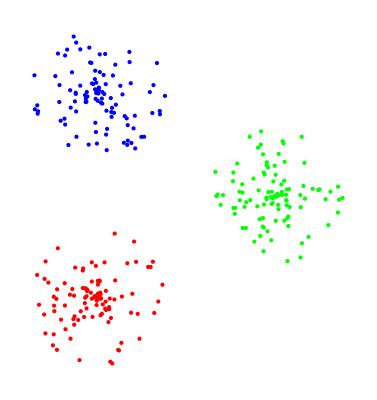

```mathematica
Graphics[Table[{col[1][[n]],pgData[1][[n]]},{n,3}]]
```

#### Data2

```mathematica
gDatasets[[2]]//Length
```

3

```mathematica
col[2]=Table[Hue[n/3//N],{n,3}]
```

{Hue[0.3333333333333333],Hue[0.6666666666666666],Hue[1.]}

```mathematica
pgData[2]=Map[Point[#]&,gDatasets[[2]],{2}];
```

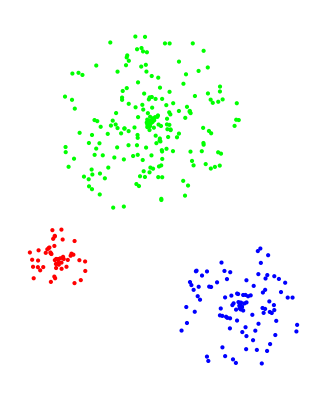

```mathematica
Graphics[Table[{col[2][[n]],pgData[2][[n]]},{n,3}]]
```

#### Data4

```mathematica
id=3
```

3

```mathematica
gDatasets[[3]]//Length
```

4

```mathematica
col[3]=Table[Hue[n/4//N],{n,4}]
```

{Hue[0.25],Hue[0.5],Hue[0.75],Hue[1.]}

```mathematica
pgData[3]=Map[Point[#]&,gDatasets[[3]],{2}];
```

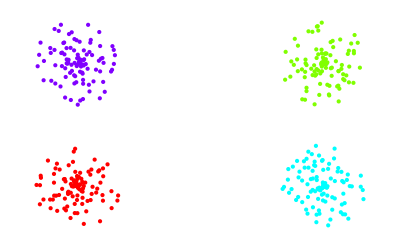

```mathematica
Graphics[Table[{col[3][[n]],pgData[3][[n]]},{n,4}]]
```

#### Data5

```mathematica
id=4
```

4

```mathematica
gDatasets[[4]]//Length
```

2

```mathematica
col[3]=Table[Hue[n/2//N],{n,2}]
```

{Hue[0.5],Hue[1.]}

```mathematica
pgData[4]=Map[Point[#]&,gDatasets[[4]],{2}];
```

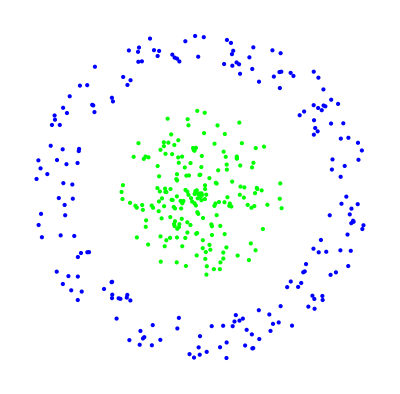

```mathematica
Graphics[Table[{col[4][[n]],pgData[4][[n]]},{n,2}]]
```

#### Data6

```mathematica
id=5
```

5

```mathematica
gDatasets[[5]]//Length
```

3

```mathematica
col[5]=Table[Hue[n/3//N],{n,3}]
```

{Hue[0.3333333333333333],Hue[0.6666666666666666],Hue[1.]}

```mathematica
pgData[5]=Map[Point[#]&,gDatasets[[5]],{2}];
```

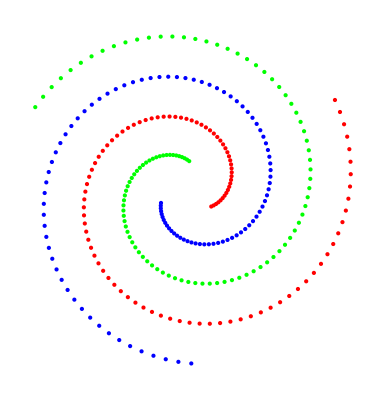

```mathematica
Graphics[Table[{col[5][[n]],pgData[5][[n]]},{n,3}]]
```

#### Data7

```mathematica
id=6
```

6

```mathematica
gDatasets[[6]]//Length
```

2

```mathematica
col[6]=Table[Hue[n/2//N],{n,2}]
```

{Hue[0.5],Hue[1.]}

```mathematica
pgData[6]=Map[Point[#]&,gDatasets[[6]],{2}];
```

```mathematica
Graphics3D[Table[{col[6][[n]],pgData[6][[n]]},{n,2}]]
```

-Graphics3D-

### Many class

```mathematica
id=10;class=8;meth="A"
```

A

```mathematica
file="/home/kamano/gitsrc/ClusteringAdequation/generative-data/data10.cl-A.8"
```

/home/kamano/gitsrc/ClusteringAdequation/generative-data/data10.cl-A.8

```mathematica
data[id,class,meth]=Import[file,"TSV"];
```

```mathematica
gData[id,class,meth]=Map[Drop[#,-1]&,Gather[data[id,class,meth],#1[[-1]]==#2[[-1]]&],{2}];
```

#### Data10

```mathematica
len=Length[gData[id,class,meth]]
```

8

```mathematica
cols=Table[Hue[n/len//N],{n,len}]
```

{Hue[0.125],Hue[0.25],Hue[0.375],Hue[0.5],Hue[0.625],Hue[0.75],Hue[0.875],Hue[1.]}

```mathematica
Graphics3D[Table[{cols[[n]],Map[Point[#]&,gData[id,class,meth][[n]]]},{n,len}]]
```

-Graphics3D-